# Fitting to the data

```mathematica
Remove["Global`*"];
```

```mathematica
SetOptions[DensityPlot,BaseStyle->{FontSize->16}];
SetOptions[Plot,BaseStyle->{FontSize->16}];
```

Adam’s requests:

1. Fit fourth moment hafnian / second moment squared vs n to b n + c log n + d for k=gamma n^a. Plot three heat maps: b,c,d as a function of a and gamma.

2. Fit c_i k^i / g(n,0,0,0) vs i/2n to Gaussian (for biggest n we have). Plot heat map of  mean,std as a function of a and gamma.

## Load precomputed g values

Using the file from the Drive file (almost 200mb!). Takes ~30 seconds.

```mathematica
gFilename="/Users/jtiosue/Desktop/computedG.csv";
```

```mathematica
g=Association@@Table[
{tup[[1]],tup[[{2,3,4}]]}->∑_(i=0)^(Length[tup]-5) tup[[5+i]] k^i,
{tup,Import@gFilename}
];
```

```mathematica
g//Length
```

49338

### All of the a={0,0,0} entries

```mathematica
ns=Select[Keys@g,#[[2]]=={0,0,0}&][[All,1]]//Sort
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}

```mathematica
(*Table[
{n,g[{n,{0,0,0}}]},
{n,ns}
]//TableForm*)
```

## Adam’s first request

Fit fourth moment hafnian / second moment squared vs n to b n + c log n + d for k=gamma n^a. Plot three heat maps: b,c,d as a function of a and gamma.

```mathematica
secondMoment[n_,k_]:= (2n-1)!! ((k+2(n-1))!!)/((k-2)!!);
fourthMoment[n_,kk_]:=(2n-1)!! g[{n,{0,0,0}}]/.k->kk;
normalizedFourthMoment[n_,k_]:=fourthMoment[n,k]/secondMoment[n,k]^2;
```

### Find b, c, d for a k = gamma n^a

```mathematica
findFitParameters[γ_,a_]:=FindFit[
Log@normalizedFourthMoment[#,γ #^a]&/@ns,
b n+c Log@n+d,
{b,c,d},
n
];
```

### Plot (param is one of b, c, d)

```mathematica
plotFun[param_,fun_]:=DensityPlot[
param/.fun[γ,a],{γ,0,3},{a,0,3},
PlotLegends->Automatic,ColorFunction->"TemperatureMap",
FrameLabel->{"γ","a"},PlotLabel->ToString@param,
ImageSize->Large
];
```

```mathematica
plotParameter[param_]:=plotFun[param,findFitParameters];
```

General::munfl: 0.000104632^78 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000104632^79 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

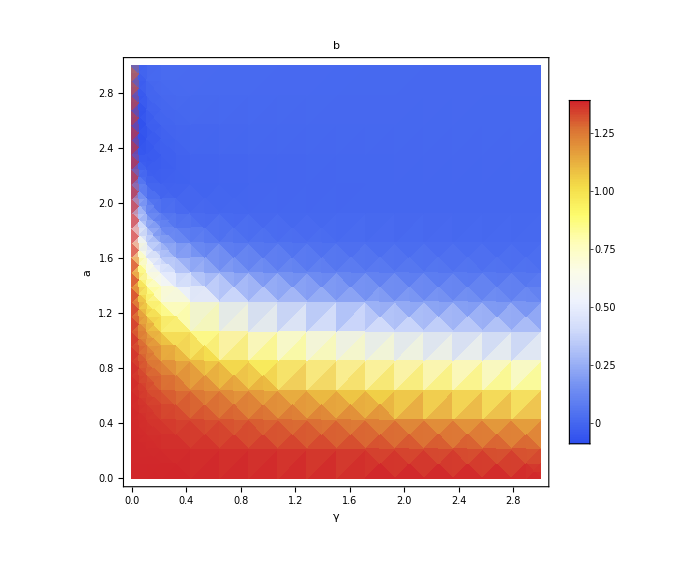

```mathematica
plotParameter@b
```

General::munfl: 0.000104632^78 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000104632^79 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

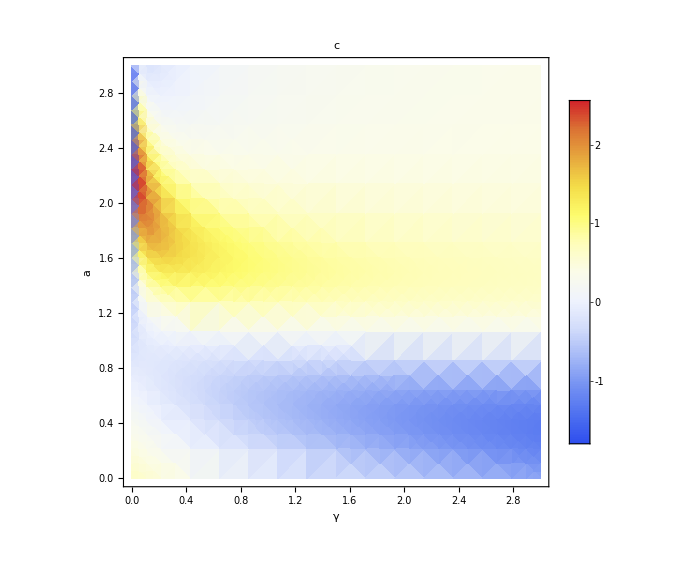

```mathematica
plotParameter@c
```

General::munfl: 0.000104632^78 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000104632^79 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

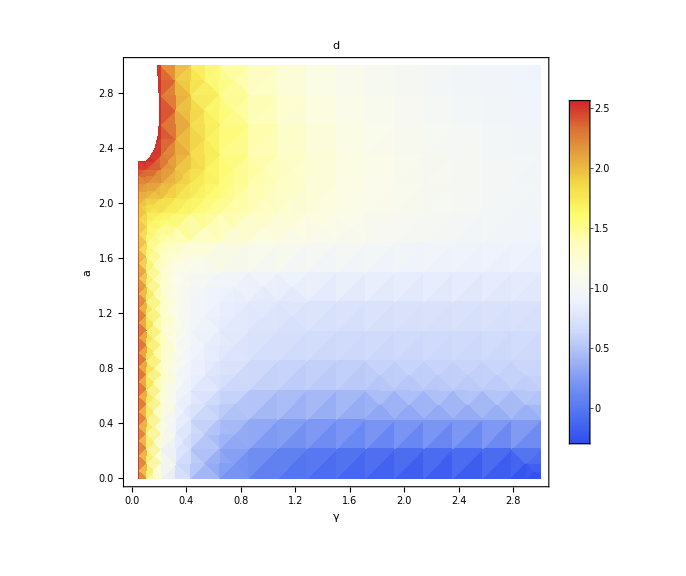

```mathematica
plotParameter@d
```

### Plot slice

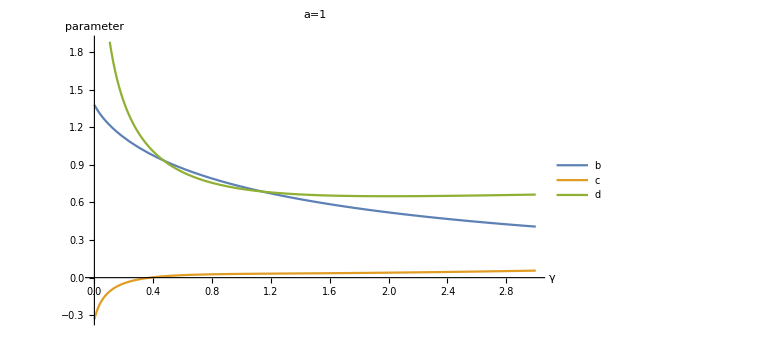

```mathematica
Plot[
{b/.findFitParameters[γ,1],c/.findFitParameters[γ,1],d/.findFitParameters[γ,1]},
{γ,0,3},
PlotLegends->{"b","c","d"},
AxesLabel->{"γ","parameter"},
PlotLabel->"a=1",
ImageSize->Large
]
```

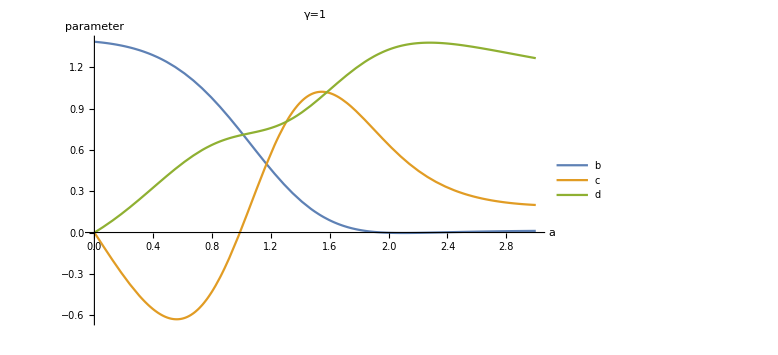

```mathematica
Plot[
{b/.findFitParameters[1,a],c/.findFitParameters[1,a],d/.findFitParameters[1,a]},
{a,0,3},
PlotLegends->{"b","c","d"},
AxesLabel->{"a","parameter"},
PlotLabel->"γ=1",
ImageSize->Large
]
```

## Adam’s second request

Fit c_i k^i / g(n,0,0,0) vs i/2n to Gaussian (for biggest n we have). Plot heat map of  mean,std as a function of a and gamma.

```mathematica
findFitMeanStd[γ_,a_]:={μ->μf/(2ns[[-1]]),σ->σf/(2ns[[-1]])}/.FindFit[
1/(g[{ns[[-1]],{0,0,0}}]/.k->(γ ns[[-1]]^a))Coefficient[g[{ns[[-1]],{0,0,0}}],k,#](γ ns[[-1]]^a)^#&/@Range[2ns[[-1]]],
1/(√(2Pi)σf)Exp[(-(i-μf)^2)/(2 σf^2)],
{μf,σf},
i
];
```

### Plot (param is one of μ,σ)

```mathematica
plotMeanStd[param_]:=plotFun[param,findFitMeanStd];
```

General::munfl: 3.46988×10^-86 3.49031×10^-228 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.39729×10^-88 7.48515×10^-232 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.21218×10^-91 1.60523×10^-235 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

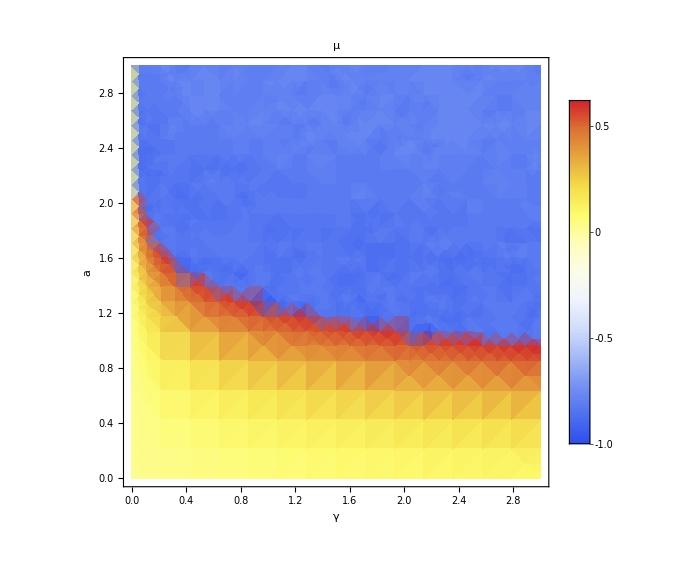

```mathematica
plotMeanStd@μ
```

General::munfl: 3.46988×10^-86 3.49031×10^-228 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.39729×10^-88 7.48515×10^-232 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.21218×10^-91 1.60523×10^-235 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

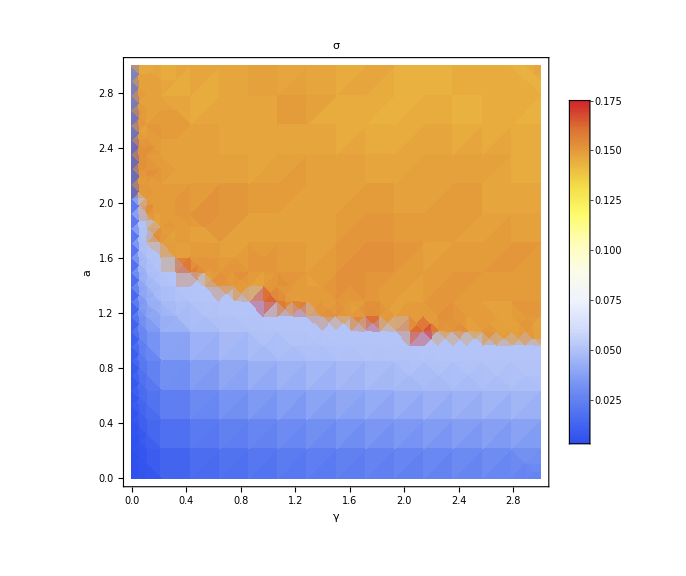

```mathematica
plotMeanStd@σ
```

### Plot slice

General::munfl: 1.40013×10^-118 6.56182×10^-194 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.59616×10^-121 1.60858×10^-196 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.52242×10^-124 3.94332×10^-199 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

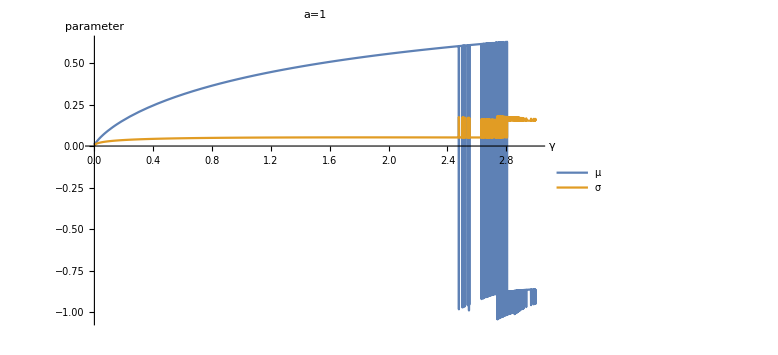

```mathematica
Plot[
{μ/.findFitMeanStd[γ,1],σ/.findFitMeanStd[γ,1]},
{γ,0,3},
PlotLegends->{"μ","σ"},
AxesLabel->{"γ","parameter"},
PlotLabel->"a=1",
ImageSize->Large
]
```

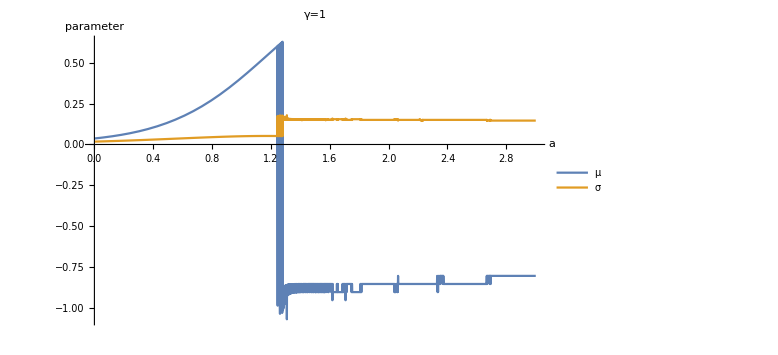

```mathematica
Plot[
{μ/.findFitMeanStd[1,a],σ/.findFitMeanStd[1,a]},
{a,0,3},
PlotLegends->{"μ","σ"},
AxesLabel->{"a","parameter"},
PlotLabel->"γ=1",
ImageSize->Large
]
```